{{uu[y]→-(2/3)^(1/3)/((-9 y+√3 √(4+27 y^2))^(1/3))+((-9 y+√3 √(4+27 y^2))^(1/3))/(2^(1/3) 3^(2/3))},{uu[y]→(1+ⅈ √3)/(2^(2/3) 3^(1/3) (-9 y+√3 √(4+27 y^2))^(1/3))-((1-ⅈ √3) (-9 y+√3 √(4+27 y^2))^(1/3))/(2 2^(1/3) 3^(2/3))},{uu[y]→(1-ⅈ √3)/(2^(2/3) 3^(1/3) (-9 y+√3 √(4+27 y^2))^(1/3))-((1+ⅈ √3) (-9 y+√3 √(4+27 y^2))^(1/3))/(2 2^(1/3) 3^(2/3))}}

1.

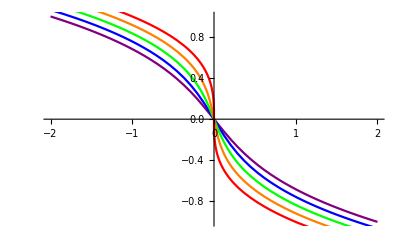

```mathematica
(* Solve the Self-Similar Burgers Equation *)
λ=1/2;1/2;1/4;1/6;
sol=DSolve[y==-uu[y]-uu[y]^(1+1/λ),{uu[y]},{y}]
U[y_]:=Evaluate[(uu[y]/.sol[[1]])]
U[-2.]
(*Plot[U[y],{y,-2,2}]*)
u[x_,t_]:=(1-t)^λ*U[x/(1-t)^(1+λ)]
Show[
Plot[u[x,0],{x,-2,2},PlotStyle->Purple],
Plot[u[x,0.25],{x,-2,2},PlotStyle->Blue],
Plot[u[x,0.5],{x,-2,2},PlotStyle->Green],
Plot[u[x,0.75],{x,-2,2},PlotStyle->Orange],
Plot[u[x,0.9999],{x,-2,2},PlotStyle->Red]
]
```

-2 (1-t)^(3/2)

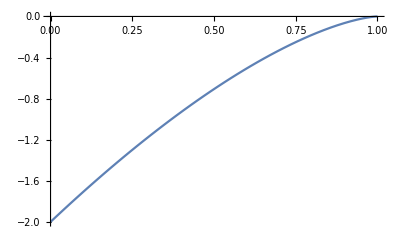

```mathematica
(*how location x where U[y[x]]==1 shrinks with time*)
boundary[t_]:=Evaluate[x/.Solve[x/(1-t)^(1+λ)==-2,x][[1]]];
boundary[t]
Plot[boundary[t],{t,0,1}]
```

```mathematica
FullSimplify[u[x,t]]
Limit[u[x,t],t->1]
Limit[u[0,t],t->1]
```

(√(1-t) (-2 3^(1/3)+2^(1/3) (-(9 x)/(1-t)^(3/2)+√(12-(81 x^2)/(-1+t)^3))^(2/3)))/(6^(2/3) (-(9 x)/(1-t)^(3/2)+√(12-(81 x^2)/(-1+t)^3))^(1/3))

Indeterminate

0